```mathematica
SetDirectory[FileNameJoin@{ParentDirectory[NotebookDirectory[]],"Shared"}];
Needs["gUtils`"];
Needs["gBRDF`"];
Needs["sgCommon`"];
Needs["gPlots`"];
Needs["gBlochSphere`"];
Needs["gPlots3D`"];
Needs["gPlots3DEx`"];
Needs["gSphericalCap`"];
Needs["gTexStyles`"];
ResetDirectory[];

ClearAll[diskCenter,diskNormal,α1,α2,radius,dr,dx,ϕ,ϕi,ϕo,QQ1,PQ1];
radius=1;
α1=ϕi;
QQ1=radius*Cos[α1];
PQ1=radius*Sin[α1];
α2=ArcTan[(dr+PQ1)/QQ1];
ϕo=α2;
dr=dx*radius;
ϕ=(ϕi+ϕo)/2-ϕi//Simplify

diskCenter=Normalize@{0,0,1};
diskNormal=Normalize@{1,0,-1.5};
Manipulate[
Show[
{
blPaperIntsDisk07[diskCenter,diskNormal,diskRadius,calcPointPercent]

 },

PlotRange->{{-1,1},{-1,1},{0,2}},
		Axes->True,Boxed->False,AspectRatio->1,ViewPoint->Front,
	    ViewProjection->"Orthographic",AxesLabel->{"X","Y","Z"},
	    ImageSize->Large
],

{{calcPointPercent,0.8},0.1,0.99},
{{diskRadius,0.6},0.1,0.6}
]
```

1/2 (-ϕi+ArcTan[dx Sec[ϕi]+Tan[ϕi]])

```mathematica
1/2 (-θL+ArcTan[k Sec[θL]+Tan[θL]])//Simplify
1/2 (-ϕi+ArcTan[Cos[ϕi] (dr1+Sin[ϕi])])
1/4 (π-2 ϕi-2 ArcTan[Sec[ϕi]/(dr1+Sin[ϕi])])//Simplify
```

1/2 (-θL+ArcTan[k Sec[θL]+Tan[θL]])

1/4 (π-2 ϕi-2 ArcTan[Sec[ϕi]/(dr1+Sin[ϕi])])

```mathematica
π/2-ArcTan[a]//FullSimplify
```

1/2 (π-2 ArcTan[a])

```mathematica
Plot3D[1/4 (π-2 ϕi-2 ArcTan[Sec[ϕi]/(dr1+Sin[ϕi])])-(1/2 (-ϕi+ArcTan[dr1 Sec[ϕi]+Tan[ϕi]])),{ϕi,0,π/2},{dr1,0.1,100}]
```

-Graphics3D-

```mathematica
1/4 (π-2 ϕi-2(π/2- ArcTan[1/(Sec[ϕi]/(dr1+Sin[ϕi]))]))//Simplify
```

1/2 (-ϕi+ArcTan[Cos[ϕi] (dr1+Sin[ϕi])])

```mathematica
1/(Sec[ϕi]/(dr1+Sin[ϕi]))
```

Cos[ϕi] (dr1+Sin[ϕi])

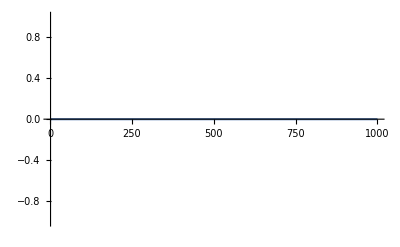

ArcTan[x]==ArcCot[1/x]

```mathematica
Plot[ArcTan[x]-ArcCot[1/x],{x,1,1000}]
ArcTan[x]==ArcCot[1/x]
```